```mathematica
(* Setup metric *)
```

```mathematica
Sigma=r^2+a^2*Cos[h]^2
Delta=r^2-2*r+a^2
(*Clear[Sigma,Delta]*)
gmetnagataki={{-1+2*r/Sigma,2*r/Sigma,0,-2*a*r*Sin[h]^2/Sigma},{2*r/Sigma,1+2*r/Sigma,0,-a*Sin[h]^2*(1+2*r/Sigma)},{0,0,Sigma,0},{-2*a*r*Sin[h]^2/Sigma,-a*Sin[h]^2*(1+2*r/Sigma),0,Sin[h]^2/Sigma*((r^2+a^2)^2-Delta*a^2*Sin[h]^2)}}
gmet={{-1+2*r/Sigma,2*r/Sigma,0,-2*a*r*Sin[h]^2/Sigma},{2*r/Sigma,1+2*r/Sigma,0,-a*Sin[h]^2*(1+2*r/Sigma)},{0,0,Sigma,0},{-2*a*r*Sin[h]^2/Sigma,-a*Sin[h]^2*(1+2*r/Sigma),0,Sin[h]^2*(Sigma+a^2*(1+2*r/Sigma)*Sin[h]^2)}}
MatrixForm[gmet]
```

r^2+a^2 Cos[h]^2

a^2-2 r+r^2

{{-1+(2 r)/(r^2+a^2 Cos[h]^2),(2 r)/(r^2+a^2 Cos[h]^2),0,-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2)},{(2 r)/(r^2+a^2 Cos[h]^2),1+(2 r)/(r^2+a^2 Cos[h]^2),0,-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2},{0,0,r^2+a^2 Cos[h]^2,0},{-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2),-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2,0,(Sin[h]^2 ((a^2+r^2)^2-a^2 (a^2-2 r+r^2) Sin[h]^2))/(r^2+a^2 Cos[h]^2)}}

{{-1+(2 r)/(r^2+a^2 Cos[h]^2),(2 r)/(r^2+a^2 Cos[h]^2),0,-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2)},{(2 r)/(r^2+a^2 Cos[h]^2),1+(2 r)/(r^2+a^2 Cos[h]^2),0,-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2},{0,0,r^2+a^2 Cos[h]^2,0},{-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2),-a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2,0,Sin[h]^2 (r^2+a^2 Cos[h]^2+a^2 (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2)}}

(-1+(2 r)/(r^2+a^2 Cos[h]^2) | (2 r)/(r^2+a^2 Cos[h]^2) | 0 | -(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2)
(2 r)/(r^2+a^2 Cos[h]^2) | 1+(2 r)/(r^2+a^2 Cos[h]^2) | 0 | -a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2
0 | 0 | r^2+a^2 Cos[h]^2 | 0
-(2 a r Sin[h]^2)/(r^2+a^2 Cos[h]^2) | -a (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2 | 0 | Sin[h]^2 (r^2+a^2 Cos[h]^2+a^2 (1+(2 r)/(r^2+a^2 Cos[h]^2)) Sin[h]^2))

```mathematica
(* compute gdet *)
```

```mathematica
FullSimplify[Det[gmet]]
FullSimplify[Det[gmetnagataki]]
mygdet=Abs[Sigma*Sin[h]]
thisgdet=Sqrt[-Det[gmet]]
nagatakigdet=Sqrt[-Det[gmet]]
FullSimplify[thisgdet-mygdet]
FullSimplify[nagatakigdet-mygdet]
```

-1/4 (a^2+2 r^2+a^2 Cos[2 h])^2 Sin[h]^2

-1/4 (a^2+2 r^2+a^2 Cos[2 h])^2 Sin[h]^2

Abs[(r^2+a^2 Cos[h]^2) Sin[h]]

√(r^4 Sin[h]^2+2 a^2 r^2 Cos[h]^2 Sin[h]^2+a^4 Cos[h]^4 Sin[h]^2)

√(r^4 Sin[h]^2+2 a^2 r^2 Cos[h]^2 Sin[h]^2+a^4 Cos[h]^4 Sin[h]^2)

-Abs[(r^2+a^2 Cos[h]^2) Sin[h]]+√((r^2+a^2 Cos[h]^2)^2 Sin[h]^2)

-Abs[(r^2+a^2 Cos[h]^2) Sin[h]]+√((r^2+a^2 Cos[h]^2)^2 Sin[h]^2)

```mathematica
(* Write down 2nd and 4th order solutions to flux *)
```

```mathematica
Li2[x_]:=-Integrate[Log[1-t*x]/t,{t,0,1}]
fofr=(Li2[2/r]-Log[1-2/r]*Log[r/2])*r^2*(2*r-3)/8+(1+3*r-6*r^2)/12*Log[r/2]+11/72+1/(3*r)+r/2-r^2/2
(*fofr=Fofr*)
Aphi0=-C*Cos[h]
Aphi2=C*fofr*Cos[h]*Sin[h]^2
Bphi1=-C/(4*r^2)*(1/2+2/r)
(* Set h1=h3=h5=b0=b2=0 since end up only being a^6 in energy flux and easier to deal with Nagataki to relevant desired order *)
h1=0
h3=0
h5=0
b0=0
b2=0
Aphi4=h1*Cos[h]+h3*Cos[h]^3+h5*Cos[h]^5
Buphi3=g0+g2*Cos[2*h]
omega1=1/8
omega3=b0+b2*Cos[2*h]
gdet=mygdet
gdet=If[h>Pi/2,Evaluate[-Sigma*Sin[h]],Evaluate[Sigma*Sin[h]]]
gdet=Sigma*Sin[h] (* only for integration from 0 to pi/2 *)
rp=1+Sqrt[1-a^2]
OmegaH=a/(2*rp)

(* Nagataki form with expansion in a *)
omega=a*omega1+a^3*omega3
Aphi=Aphi0+a^2*Aphi2+a^4*Aphi4
Br=D[Aphi,h]/gdet
(* Enforce total flux to be constant *)
Print["Result of fixing flux"];
sols=Solve[fluxC==Integrate[Br*gdet,{h,0,Pi/2}],C]
Aphi=Aphi//.sols[[1]]
(* recompute Br *)
Print["Nagataki version of Br"];
Br=D[Aphi,h]/gdet
FE=(2*Br^2*omega*rp*(OmegaH-omega)*Sin[h]^2)//.{r->rp}
sFE=Series[FE,{a,0,4}]
(* Integrate up to finite angle: Ensure to compare factors of 2X correctly when only including one hemisophere *)
Edot=Integrate[sdEdot,{h,0,he}]
Edotlist=CoefficientList[Edot,a]
Edotfull=Edot//.{he->Pi/2}
powernagataki=C^2*(Pi/24)*a^2(1+1/45(56-3 Pi^2)a^2)
FullSimplify[(Edotfull-powernagataki)]
(* Above is 0, so I agree with Nagataki's paper shown result *)

(* omegah^2 form of expansion of A_\phi up to a^2 order *)
(* Choose omega to be omegaH/2 *)
myomega=OmegaH/2
myAphi=Aphi0+aphicoef*OmegaH^2*Aphi2
(* Enforce A_phi in omegah form to be same as A_\phi in $a$ form to a^2 order *)
lhs=CoefficientList[Normal[Series[Aphi//.{r->rp},{a,0,2}]],a]
rhs=CoefficientList[Normal[Series[myAphi//.{r->rp},{a,0,2}]],a]
Print["Below is result of coefficient assignment between Nagataki Aphi and omegah version of Aphi for a^2 term.  Has no angle dependence, so consistent without any trouble."];
sols=Solve[lhs[[3]]==rhs[[3]],aphicoef]
myAphi=myAphi//.sols[[1]]
myBr=D[myAphi,h]/gdet
(* Enforce total flux to be constant *)
Print["Result of fixing flux"];
sols=Solve[fluxC==Integrate[myBr*gdet,{h,0,Pi/2}],C]
myAphi=myAphi//.sols[[1]]
(* recompute Br *)
Print["omegah version of Br"];
myBr=D[myAphi,h]/gdet
(* Get final total energy flux with new Br *)
myFE=(2*myBr^2*myomega*rp*(OmegaH-myomega)*Sin[h]^2)//.{r->rp}
mysFE=Series[myFE,{a,0,4}]
(* Note that since myBr and myomega are consistent with Nagataki to lowest order, this myFE should be automatically consistent at the a^4 order, but still check *)
Print["If below ia O[a^5], then final myFE is consistent with Nagataki to a^4 order"];
FullSimplify[(sFE-mysFE)//.{fluxC->C},{-1≤a≤1}]
```

11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])

-C Cos[h]

C Cos[h] (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^2

-(C (1/2+2/r))/(4 r^2)

0

0

0

«3 more identical outputs»

g0+g2 Cos[2 h]

1/8

0

Abs[(r^2+a^2 Cos[h]^2) Sin[h]]

If[h>π/2,(-r^2-a^2 Cos[h]^2) Sin[h],(r^2+a^2 Cos[h]^2) Sin[h]]

(r^2+a^2 Cos[h]^2) Sin[h]

1+√(1-a^2)

a/(2 (1+√(1-a^2)))

a/8

-C Cos[h]+a^2 C Cos[h] (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^2

1/(r^2+a^2 Cos[h]^2)Csc[h] (C Sin[h]+2 a^2 C Cos[h]^2 (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]-a^2 C (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^3)

Result of fixing flux

{{C→fluxC}}

-fluxC Cos[h]+a^2 fluxC Cos[h] (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^2

Nagataki version of Br

1/(r^2+a^2 Cos[h]^2)Csc[h] (fluxC Sin[h]+2 a^2 fluxC Cos[h]^2 (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]-a^2 fluxC (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^3)

1/(4 ((1+√(1-a^2))^2+a^2 Cos[h]^2)^2)a (1+√(1-a^2)) (-a/8+a/(2 (1+√(1-a^2)))) (fluxC Sin[h]+2 a^2 fluxC Cos[h]^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]-a^2 fluxC (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]^3)^2

(1/256 fluxC^2 Sin[h]^2 a^2+((45 fluxC^2 Sin[h]^2-116 fluxC^2 Cos[h]^2 Sin[h]^2+12 fluxC^2 π^2 Cos[h]^2 Sin[h]^2+49 fluxC^2 Sin[h]^4-6 fluxC^2 π^2 Sin[h]^4) a^4)/9216+O[a]^6)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] (-1/256 ⅈ fluxC^2 π Cos[h]^2 Sin[h]^2 a^6-(ⅈ (9 fluxC^2 π Cos[h]^2 Sin[h]^2-134 fluxC^2 π Cos[h]^4 Sin[h]^2+12 fluxC^2 π^3 Cos[h]^4 Sin[h]^2+49 fluxC^2 π Cos[h]^2 Sin[h]^4-6 fluxC^2 π^3 Cos[h]^2 Sin[h]^4) a^8)/18432+O[a]^9)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-1/256 ⅈ fluxC^2 π Cos[h]^2 Sin[h]^2 a^6-(ⅈ (9 fluxC^2 π Cos[h]^2 Sin[h]^2-134 fluxC^2 π Cos[h]^4 Sin[h]^2+12 fluxC^2 π^3 Cos[h]^4 Sin[h]^2+49 fluxC^2 π Cos[h]^2 Sin[h]^4-6 fluxC^2 π^3 Cos[h]^2 Sin[h]^4) a^8)/18432+O[a]^9)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-1/512 (fluxC^2 π^2 Cos[h]^4 Sin[h]^2) a^10+((2 fluxC^2 π^2 Cos[h]^4 Sin[h]^2+fluxC^2 π^2 Cos[h]^6 Sin[h]^2) a^12)/1024+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 (-((fluxC^2 π^2 Cos[h]^4 Sin[h]^2) a^10)/1024+((2 fluxC^2 π^2 Cos[h]^4 Sin[h]^2+fluxC^2 π^2 Cos[h]^6 Sin[h]^2) a^12)/2048+O[a]^13)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 (-((fluxC^2 π^2 Cos[h]^4 Sin[h]^2) a^10)/1024+((2 fluxC^2 π^2 Cos[h]^4 Sin[h]^2+fluxC^2 π^2 Cos[h]^6 Sin[h]^2) a^12)/2048+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] (1/512 ⅈ fluxC^2 π Sin[h]^4 a^6+(ⅈ (9 fluxC^2 π Sin[h]^4-134 fluxC^2 π Cos[h]^2 Sin[h]^4+12 fluxC^2 π^3 Cos[h]^2 Sin[h]^4+49 fluxC^2 π Sin[h]^6-6 fluxC^2 π^3 Sin[h]^6) a^8)/36864+O[a]^9)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (1/512 ⅈ fluxC^2 π Sin[h]^4 a^6+(ⅈ (9 fluxC^2 π Sin[h]^4-134 fluxC^2 π Cos[h]^2 Sin[h]^4+12 fluxC^2 π^3 Cos[h]^2 Sin[h]^4+49 fluxC^2 π Sin[h]^6-6 fluxC^2 π^3 Sin[h]^6) a^8)/36864+O[a]^9)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 ((fluxC^2 π^2 Cos[h]^2 Sin[h]^4 a^10)/1024+((-2 fluxC^2 π^2 Cos[h]^2 Sin[h]^4-fluxC^2 π^2 Cos[h]^4 Sin[h]^4) a^12)/2048+O[a]^13)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 ((fluxC^2 π^2 Cos[h]^2 Sin[h]^4 a^10)/1024+((-2 fluxC^2 π^2 Cos[h]^2 Sin[h]^4-fluxC^2 π^2 Cos[h]^4 Sin[h]^4) a^12)/2048+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (1/512 fluxC^2 π^2 Cos[h]^2 Sin[h]^4 a^10+((-2 fluxC^2 π^2 Cos[h]^2 Sin[h]^4-fluxC^2 π^2 Cos[h]^4 Sin[h]^4) a^12)/1024+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-((fluxC^2 π^2 Sin[h]^6) a^10)/2048+((2 fluxC^2 π^2 Sin[h]^6+fluxC^2 π^2 Cos[h]^2 Sin[h]^6) a^12)/4096+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 (-((fluxC^2 π^2 Sin[h]^6) a^10)/4096+((2 fluxC^2 π^2 Sin[h]^6+fluxC^2 π^2 Cos[h]^2 Sin[h]^6) a^12)/8192+O[a]^13)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 (-((fluxC^2 π^2 Sin[h]^6) a^10)/4096+((2 fluxC^2 π^2 Sin[h]^6+fluxC^2 π^2 Cos[h]^2 Sin[h]^6) a^12)/8192+O[a]^13)

(a^2 C^2 π (20 (36+a^2 (-2+3 π^2))+5 (72+a^2 (-238+33 π^2)) Cos[he]+9 a^2 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/4320

{0,0,1/6 C^2 π Sin[he/2]^4+1/12 C^2 π Cos[he] Sin[he/2]^4,0,1/216 C^2 π (-2+3 π^2) Sin[he/2]^4+1/864 C^2 π (-238+33 π^2) Cos[he] Sin[he/2]^4+1/480 C^2 π (-26+3 π^2) (4 Cos[2 he]+Cos[3 he]) Sin[he/2]^4}

(a^2 C^2 π (-36 a^2 (-26+3 π^2)+20 (36+a^2 (-2+3 π^2))))/17280

1/24 a^2 C^2 π (1+1/45 a^2 (56-3 π^2))

0

a/(4 (1+√(1-a^2)))

-C Cos[h]+(a^2 aphicoef C Cos[h] (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^2)/(4 (1+√(1-a^2))^2)

{-fluxC Cos[h],0,1/72 fluxC (-49+6 π^2) Cos[h] Sin[h]^2,0,-1/4 ⅈ fluxC π Cos[h] Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Sin[h]^2-1/4 ⅈ fluxC π Cos[h] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] Sin[h]^2}

{-C Cos[h],0,(aphicoef C (-49+6 π^2) Cos[h] Sin[h]^2)/1152,0,-1/64 ⅈ aphicoef C π Cos[h] Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Sin[h]^2-1/64 ⅈ aphicoef C π Cos[h] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] Sin[h]^2}

Below is result of coefficient assignment between Nagataki Aphi and omegah version of Aphi for a^2 term.  Has no angle dependence, so consistent without any trouble.

{{aphicoef→(16 fluxC)/C}}

-C Cos[h]+(4 a^2 fluxC Cos[h] (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^2)/((1+√(1-a^2))^2)

(Csc[h] (C Sin[h]+(8 a^2 fluxC Cos[h]^2 (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h])/((1+√(1-a^2))^2)-(4 a^2 fluxC (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^3)/((1+√(1-a^2))^2)))/(r^2+a^2 Cos[h]^2)

Result of fixing flux

{{C→fluxC}}

-fluxC Cos[h]+(4 a^2 fluxC Cos[h] (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^2)/((1+√(1-a^2))^2)

omegah version of Br

(Csc[h] (fluxC Sin[h]+(8 a^2 fluxC Cos[h]^2 (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h])/((1+√(1-a^2))^2)-(4 a^2 fluxC (11/72+1/(3 r)+r/2-r^2/2+1/12 (1+3 r-6 r^2) Log[r/2]+1/8 r^2 (-3+2 r) (-Log[1-2/r] Log[r/2]+PolyLog[2,2/r])) Sin[h]^3)/((1+√(1-a^2))^2)))/(r^2+a^2 Cos[h]^2)

1/(8 (1+√(1-a^2)) ((1+√(1-a^2))^2+a^2 Cos[h]^2)^2)a^2 (fluxC Sin[h]+1/((1+√(1-a^2))^2)8 a^2 fluxC Cos[h]^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]-1/((1+√(1-a^2))^2)4 a^2 fluxC (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]^3)^2

Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] (-1/256 ⅈ fluxC^2 π Cos[h]^2 Sin[h]^2 a^6+O[a]^8)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-1/256 ⅈ fluxC^2 π Cos[h]^2 Sin[h]^2 a^6+O[a]^8)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-1/512 (fluxC^2 π^2 Cos[h]^4 Sin[h]^2) a^10+O[a]^12)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 (-((fluxC^2 π^2 Cos[h]^4 Sin[h]^2) a^10)/1024+O[a]^12)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 (-((fluxC^2 π^2 Cos[h]^4 Sin[h]^2) a^10)/1024+O[a]^12)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] (1/512 ⅈ fluxC^2 π Sin[h]^4 a^6+O[a]^8)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (1/512 ⅈ fluxC^2 π Sin[h]^4 a^6+O[a]^8)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 ((fluxC^2 π^2 Cos[h]^2 Sin[h]^4 a^10)/1024+O[a]^12)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 ((fluxC^2 π^2 Cos[h]^2 Sin[h]^4 a^10)/1024+O[a]^12)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (1/512 fluxC^2 π^2 Cos[h]^2 Sin[h]^4 a^10+O[a]^12)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-((fluxC^2 π^2 Sin[h]^6) a^10)/2048+O[a]^12)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 (-((fluxC^2 π^2 Sin[h]^6) a^10)/4096+O[a]^12)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 (-((fluxC^2 π^2 Sin[h]^6) a^10)/4096+O[a]^12)+(1/256 fluxC^2 Sin[h]^2 a^2+((45 fluxC^2 Sin[h]^2-116 fluxC^2 Cos[h]^2 Sin[h]^2+12 fluxC^2 π^2 Cos[h]^2 Sin[h]^2+49 fluxC^2 Sin[h]^4-6 fluxC^2 π^2 Sin[h]^4) a^4)/9216+O[a]^5)

If below ia O[a^5], then final myFE is consistent with Nagataki to a^4 order

O[a]^5

0

{0.25}

{0.25}

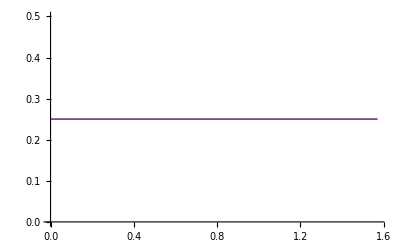

0.99

{1.11207+0. ⅈ}

{0.177452+0. ⅈ}

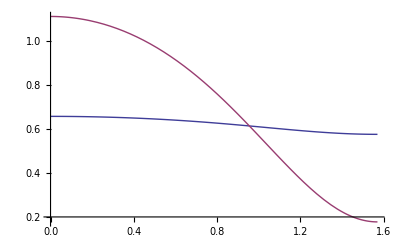

1.

{1.67284+0. ⅈ}

{-0.172842+0. ⅈ}

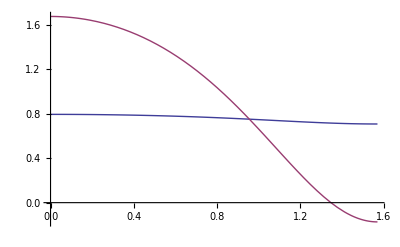

```mathematica
(* Check behavior of Br at a=0 and a=1 for Nagataki and omegah version of Br *)
mya=0
Brpolehor=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->0}]]
Brpoleeq=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->Pi/2}]]
toplot1=Br//.{r->rp,fluxC->1,a->mya};
toplot2=myBr//.{r->rp,fluxC->1,a->mya};
Plot[{toplot1,toplot2},{h,0,Pi/2}]

mya=0.99
Brpolehor=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->0}]]
Brpoleeq=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->Pi/2}]]
toplot1=Br//.{r->rp,fluxC->1,a->mya};
toplot2=myBr//.{r->rp,fluxC->1,a->mya};
Plot[{toplot1,toplot2},{h,0,Pi/2}]

mya=1.0
Brpolehor=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->0}]]
Brpoleeq=N[Limit[myBr//.{r->rp,fluxC->1,a->mya},{h->Pi/2}]]
toplot1=Br//.{r->rp,fluxC->1,a->mya};
toplot2=myBr//.{r->rp,fluxC->1,a->mya};
Plot[{toplot1,toplot2},{h,0,Pi/2}]
```

```mathematica
(* Get omegah^2 version of Br @ pole @ horizon directly without using Aphi *)
Brhor=Br//.{r->rp}
Bpolehor=Limit[Brhor,h->0]
Bpolehorseries=Normal[FullSimplify[Series[Bpolehor,{a,0,2}],{-1≤a≤1}]]
eq=fluxC==Integrate[Normal[Series[gdet*Bpolehor//.{r->rp},{a,0,2}]],{h,0,Pi/2}]
sols=Solve[eq,C]
Bpolehorseries=Normal[Series[Bpolehorseries//.sols[[1]],{a,0,2}]]
newBpolehor=C*(1/4+Brcoef*OmH^2)//.{OmH->a/(2*rp)}
newBpolehorseries=Normal[Series[newBpolehor,{a,0,2}]]

Print["Match coefficients so agrees very close to a=0"];
lefthand=CoefficientList[Bpolehorseries,a][[3]]
righthand=CoefficientList[newBpolehorseries,a][[3]]
sols=Solve[lefthand==righthand,Brcoef]
Print["Final omegah^2 version of Br at pole on horizon"];
finalnewBpolehor=newBpolehor//.sols[[1]]
eq=fluxC==Integrate[Normal[Series[gdet*finalnewBpolehor//.{r->rp},{a,0,2}]],{h,0,Pi/2}]
sols=Solve[eq,C]
finalnewBpolehor=finalnewBpolehor//.sols[[1]]

Print["Look at a=0, a=1 old, and a=1 new values of Br at pole at horizon"];
N[Bpolehorseries//.{a->0}]
N[Bpolehorseries//.{a->1}]
N[finalnewBpolehor//.{a->1}]
Print["Print ratio of new Br(a=1) to Br(a=0) at equator"];
ratio=(N[finalnewBpolehor//.{a->1}]/N[Bpolehorseries//.{a->0}])
```

1/((1+√(1-a^2))^2+a^2 Cos[h]^2)Csc[h] (C Sin[h]+2 a^2 C Cos[h]^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]-a^2 C (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]^3+a^4 (-h1 Sin[h]-3 h3 Cos[h]^2 Sin[h]-5 h5 Cos[h]^4 Sin[h]))

1/(2+2 √(1-a) √(1+a))(C-(25 a^2 C)/36+a^4 C-√(1-a) a^2 √(1+a) C+(2 a^2 C)/(3 (1+√(1-a) √(1+a)))-a^4 h1-3 a^4 h3-5 a^4 h5+1/6 a^2 (1+3 (1+√(1-a) √(1+a))-6 (1+√(1-a) √(1+a))^2) C (-Log[2]+Log[1+√(1-a) √(1+a)])-1/4 a^2 (1+√(1-a) √(1+a))^2 (-3+2 (1+√(1-a) √(1+a))) C (-Log[2]+Log[1+√(1-a) √(1+a)]) Log[1-2/(1+√(1-a) √(1+a))]+((a^2 C)/2-(3 a^4 C)/4+1/2 √(1-a) a^2 √(1+a) C-1/2 √(1-a) a^4 √(1+a) C) PolyLog[2,2/(1+√(1-a) √(1+a))])

C/4+1/72 a^2 C (-20+3 π^2)

fluxC==1/36 C (36+a^2 (-55+6 π^2))

{{C→(36 fluxC)/(36-55 a^2+6 a^2 π^2)}}

fluxC/4+(5 a^2 fluxC)/48

(1/4+(a^2 Brcoef)/(4 (1+√(1-a^2))^2)) C

C/4+1/16 a^2 Brcoef C

Match coefficients so agrees very close to a=0

(5 fluxC)/48

(Brcoef C)/16

{{Brcoef→(5 fluxC)/(3 C)}}

Final omegah^2 version of Br at pole on horizon

C (1/4+(5 a^2 fluxC)/(12 (1+√(1-a^2))^2 C))

fluxC==C-(5 a^2 C)/12+(5 a^2 fluxC)/12

{{C→fluxC}}

(1/4+(5 a^2)/(12 (1+√(1-a^2))^2)) fluxC

Look at a=0, a=1 old, and a=1 new values of Br at pole at horizon

0.25 fluxC

0.354167 fluxC

0.666667 fluxC

Print ratio of new Br(a=1) to Br(a=0) at equator

2.66667

```mathematica
(* Get omegah^2 version of Br @ equator @ horizon *)
Brhor=Br//.{r->rp}
Bpolehor=Limit[Brhor,h->Pi/2]
Bpolehorseries=Normal[FullSimplify[Series[Bpolehor,{a,0,2}],{-1≤a≤1}]]
eq=fluxC==Integrate[Normal[Series[gdet*Bpolehor//.{r->rp},{a,0,2}]],{h,0,Pi/2}]
sols=Solve[eq,C]
Bpolehorseries=Normal[Series[Bpolehorseries//.sols[[1]],{a,0,2}]]
newBpolehor=C*(1/4+Brcoef*OmH^2)//.{OmH->a/(2*rp)}
newBpolehorseries=Normal[Series[newBpolehor,{a,0,2}]]

Print["Match coefficients so agrees very close to a=0"];
lefthand=CoefficientList[Bpolehorseries,a][[3]]
righthand=CoefficientList[newBpolehorseries,a][[3]]
sols=Solve[lefthand==righthand,Brcoef]
Print["Final omegah^2 version of Br at equator on horizon"];
finalnewBpolehor=newBpolehor//.sols[[1]]
eq=fluxC==Integrate[Normal[Series[gdet*finalnewBpolehor//.{r->rp},{a,0,2}]],{h,0,Pi/2}]
sols=Solve[eq,C]
finalnewBpolehor=finalnewBpolehor//.sols[[1]]

Print["Look at a=0, a=1 old, and a=1 new values of Br at equator at horizon"];
N[Bpolehorseries//.{a->0}]
N[Bpolehorseries//.{a->1}]
N[finalnewBpolehor//.{a->1}]
Print["Print ratio of new Br(a=1) to Br(a=0) at equator"];
ratio=(N[finalnewBpolehor//.{a->1}]/N[Bpolehorseries//.{a->0}])
```

1/((1+√(1-a^2))^2+a^2 Cos[h]^2)Csc[h] (C Sin[h]+2 a^2 C Cos[h]^2 (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]-a^2 C (11/72+1/(3 (1+√(1-a^2)))+1/2 (1+√(1-a^2))-1/2 (1+√(1-a^2))^2+1/12 (1+3 (1+√(1-a^2))-6 (1+√(1-a^2))^2) Log[1/2 (1+√(1-a^2))]+1/8 (1+√(1-a^2))^2 (-3+2 (1+√(1-a^2))) (-Log[1/2 (1+√(1-a^2))] Log[1-2/(1+√(1-a^2))]+PolyLog[2,2/(1+√(1-a^2))])) Sin[h]^3+a^4 (-h1 Sin[h]-3 h3 Cos[h]^2 Sin[h]-5 h5 Cos[h]^4 Sin[h]))

1/(1+√(1-a) √(1+a))^2(C+(25 a^2 C)/72-(a^4 C)/2+1/2 √(1-a) a^2 √(1+a) C-(a^2 C)/(3 (1+√(1-a) √(1+a)))-a^4 h1+1/12 a^2 (-8+6 a^2-9 √(1-a) √(1+a)) C (Log[2]-Log[1+√(1-a) √(1+a)])-1/8 a^2 (1+√(1-a) √(1+a))^2 (-1+2 √(1-a) √(1+a)) C (Log[2]-Log[1+√(1-a) √(1+a)]) Log[1-2/(1+√(1-a) √(1+a))]+(-(a^2 C)/4+(3 a^4 C)/8-1/4 √(1-a) a^2 √(1+a) C+1/4 √(1-a) a^4 √(1+a) C) PolyLog[2,2/(1+√(1-a) √(1+a))])

C/4+1/288 a^2 C (85-6 π^2)

fluxC==1/72 C (72+a^2 (55-6 π^2))

{{C→-(72 fluxC)/(-72-55 a^2+6 a^2 π^2)}}

fluxC/4+(5 a^2 fluxC)/48

(1/4+(a^2 Brcoef)/(4 (1+√(1-a^2))^2)) C

C/4+1/16 a^2 Brcoef C

Match coefficients so agrees very close to a=0

(5 fluxC)/48

(Brcoef C)/16

{{Brcoef→(5 fluxC)/(3 C)}}

Final omegah^2 version of Br at equator on horizon

C (1/4+(5 a^2 fluxC)/(12 (1+√(1-a^2))^2 C))

fluxC==C-(5 a^2 C)/12+(5 a^2 fluxC)/12

{{C→fluxC}}

(1/4+(5 a^2)/(12 (1+√(1-a^2))^2)) fluxC

Look at a=0, a=1 old, and a=1 new values of Br at equator at horizon

0.25 fluxC

0.354167 fluxC

0.666667 fluxC

Print ratio of new Br(a=1) to Br(a=0) at equator

2.66667

```mathematica
(* do both hemispheres, so only integrate to pi/2 at most *)
dEdot=2*2*Pi*sFE*gdet//.{r->rp}
ordera=4
sdEdot=FullSimplify[Normal[Series[dEdot,{a,0,ordera}]],{-1≤a≤1}]
```

4 π ((1+√(1-a^2))^2+a^2 Cos[h]^2) ((1/256 C^2 Sin[h]^2 a^2+((45 C^2 Sin[h]^2-116 C^2 Cos[h]^2 Sin[h]^2+12 C^2 π^2 Cos[h]^2 Sin[h]^2+49 C^2 Sin[h]^4-6 C^2 π^2 Sin[h]^4) a^4)/9216+O[a]^6)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] (-1/256 ⅈ C^2 π Cos[h]^2 Sin[h]^2 a^6-(ⅈ (9 C^2 π Cos[h]^2 Sin[h]^2-134 C^2 π Cos[h]^4 Sin[h]^2+12 C^2 π^3 Cos[h]^4 Sin[h]^2+49 C^2 π Cos[h]^2 Sin[h]^4-6 C^2 π^3 Cos[h]^2 Sin[h]^4) a^8)/18432+O[a]^9)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-1/256 ⅈ C^2 π Cos[h]^2 Sin[h]^2 a^6-(ⅈ (9 C^2 π Cos[h]^2 Sin[h]^2-134 C^2 π Cos[h]^4 Sin[h]^2+12 C^2 π^3 Cos[h]^4 Sin[h]^2+49 C^2 π Cos[h]^2 Sin[h]^4-6 C^2 π^3 Cos[h]^2 Sin[h]^4) a^8)/18432+O[a]^9)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-1/512 (C^2 π^2 Cos[h]^4 Sin[h]^2) a^10+((2 C^2 π^2 Cos[h]^4 Sin[h]^2+C^2 π^2 Cos[h]^6 Sin[h]^2) a^12)/1024+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 (-((C^2 π^2 Cos[h]^4 Sin[h]^2) a^10)/1024+((2 C^2 π^2 Cos[h]^4 Sin[h]^2+C^2 π^2 Cos[h]^6 Sin[h]^2) a^12)/2048+O[a]^13)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 (-((C^2 π^2 Cos[h]^4 Sin[h]^2) a^10)/1024+((2 C^2 π^2 Cos[h]^4 Sin[h]^2+C^2 π^2 Cos[h]^6 Sin[h]^2) a^12)/2048+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] (1/512 ⅈ C^2 π Sin[h]^4 a^6+(ⅈ (9 C^2 π Sin[h]^4-134 C^2 π Cos[h]^2 Sin[h]^4+12 C^2 π^3 Cos[h]^2 Sin[h]^4+49 C^2 π Sin[h]^6-6 C^2 π^3 Sin[h]^6) a^8)/36864+O[a]^9)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (1/512 ⅈ C^2 π Sin[h]^4 a^6+(ⅈ (9 C^2 π Sin[h]^4-134 C^2 π Cos[h]^2 Sin[h]^4+12 C^2 π^3 Cos[h]^2 Sin[h]^4+49 C^2 π Sin[h]^6-6 C^2 π^3 Sin[h]^6) a^8)/36864+O[a]^9)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 ((C^2 π^2 Cos[h]^2 Sin[h]^4 a^10)/1024+((-2 C^2 π^2 Cos[h]^2 Sin[h]^4-C^2 π^2 Cos[h]^4 Sin[h]^4) a^12)/2048+O[a]^13)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 ((C^2 π^2 Cos[h]^2 Sin[h]^4 a^10)/1024+((-2 C^2 π^2 Cos[h]^2 Sin[h]^4-C^2 π^2 Cos[h]^4 Sin[h]^4) a^12)/2048+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (1/512 C^2 π^2 Cos[h]^2 Sin[h]^4 a^10+((-2 C^2 π^2 Cos[h]^2 Sin[h]^4-C^2 π^2 Cos[h]^4 Sin[h]^4) a^12)/1024+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)] Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)] (-((C^2 π^2 Sin[h]^6) a^10)/2048+((2 C^2 π^2 Sin[h]^6+C^2 π^2 Cos[h]^2 Sin[h]^6) a^12)/4096+O[a]^13)+Floor[(π-2 Arg[a]-Arg[(-1+√(1-a^2))/(a^2 (1+√(1-a^2)))])/(2 π)]^2 (-((C^2 π^2 Sin[h]^6) a^10)/4096+((2 C^2 π^2 Sin[h]^6+C^2 π^2 Cos[h]^2 Sin[h]^6) a^12)/8192+O[a]^13)+Floor[Arg[(-4+a^2+4 √(1-a^2)+a^2 √(1-a^2))/(a^2 (1+√(1-a^2)))]/(2 π)]^2 (-((C^2 π^2 Sin[h]^6) a^10)/4096+((2 C^2 π^2 Sin[h]^6+C^2 π^2 Cos[h]^2 Sin[h]^6) a^12)/8192+O[a]^13)) Sin[h]

4

1/576 a^2 C^2 π (36+a^2 (-2+3 π^2)+3 a^2 (-26+3 π^2) Cos[2 h]) Sin[h]^3

```mathematica
(* coefficient*)
coef=(C^2*Pi/24);
(*coef=C^2;*)
(* Numerical jet power from the simulation, nu = 0, for different spins *)
(* datax = a *)
(* datay = Power *)
datax={0.1,0.2,0.3,0.5,0.7,0.9,0.94,0.97,0.99,0.99769,0.999,0.999769,0.9999};
datay=coef*{0.00065565895056352,0.00266977190040052,0.00619285088032484,0.0191088989377022,0.0451582334935665,0.106693923473358,0.131530806422234,0.158286243677139,0.184633031487465,0.198393896222115,0.200842335820198,0.202311635017395,0.202582076191902};

a2OmH[a_]:=a/(2(1+Sqrt[1-a^2]));
OmH2a[OmH_]:=(4 OmH)/(1+4 OmH^2);
pwr0anal=coef*2Pi 0.0104167 (4OmH)^2  (* <- analytical expression for monopole BZ from BZ paper with a -> 4 OmH *)
pwrfullanal=coef*2Pi 0.0104167 (4OmH)^2(1+alpha OmH^2+beta OmH^4) (* <- analytical BZ plus high-order corrections *)
(* create a table for fitting data and fit the data *)
(* fit only deviations from the expected quadratic dependece on OmegaH: *)
varres=Table[a2OmH[datax[[i]]],{i,1,Length[datax]}]
fun1=Table[datay[[i]],{i,1,Length[datax]}]
fun2=Table[(pwr0anal/.{gamma->1,OmH->a2OmH[datax[[i]]]}),{i,1,Length[datax]}]
funres=fun1-fun2;
data=Table[{varres[[i]],funres[[i]]},{i,1,Length[datax]}];
Print["fit residual"];
res=Fit[data,{OmH^4,OmH^6},OmH]
(* find the corresponding best-fit alpha and beta coefficients of the expansion: *)
clist=CoefficientList[Collect[res-(pwrfullanal-pwr0anal),OmH],OmH]
bestfit=FullSimplify[Solve[clist==0,{alpha,beta}]][[1]]
(* expansion with the best-fit values of coefficients: *)
pwranal=coef*(OmH^2(1+alpha OmH^2-beta OmH^4)/.bestfit)
```

0.137078 C^2 OmH^2

0.137078 C^2 OmH^2 (1+alpha OmH^2+beta OmH^4)

{0.0250628,0.0505103,0.076768,0.133975,0.204184,0.313395,0.350439,0.390152,0.433804,0.467113,0.478123,0.489367,0.492978}

{0.0000858256 C^2,0.000349472 C^2,0.000810642 C^2,0.00250135 C^2,0.0059112 C^2,0.0139662 C^2,0.0172173 C^2,0.0207196 C^2,0.0241684 C^2,0.0259697 C^2,0.0262902 C^2,0.0264825 C^2,0.0265179 C^2}

{0.000086105 C^2,0.000349726 C^2,0.000807847 C^2,0.00246044 C^2,0.00571493 C^2,0.0134633 C^2,0.0168343 C^2,0.0208659 C^2,0.0257962 C^2,0.0299098 C^2,0.0313363 C^2,0.0328275 C^2,0.0333138 C^2}

fit residual

0.176879 C^2 OmH^4-1.19752 C^2 OmH^6

{0,0,0. C^2,0,0.176879 C^2-0.137078 alpha C^2,0,-1.19752 C^2-0.137078 beta C^2}

{alpha→1.29035,beta→-8.73607}

1/24 C^2 OmH^2 (1+1.29035 OmH^2+8.73607 OmH^4) π

```mathematica
(* Nagataki's expansion in terms of a: *)
powernagatakiina=Series[powernagataki,{a,0,4}]
(* Look for an equivalent expansion in terms of OmegaH: *)
powersashainomegah=C^2*(Pi/24)*((4OmH)^2(1+alpha OmH^2))
powersashainomegahina=C^2*(Pi/24)*((4OmH)^2(1+alpha OmH^2))/.{OmH->a2OmH[a]}
powersashaina=Series[powersashainomegahina,{a,0,4}]
```

1/24 C^2 π a^2+((7 C^2 π)/135-(C^2 π^3)/360) a^4+O[a]^5

2/3 C^2 OmH^2 (1+alpha OmH^2) π

(a^2 (1+(a^2 alpha)/(4 (1+√(1-a^2))^2)) C^2 π)/(6 (1+√(1-a^2))^2)

1/24 C^2 π a^2+1/384 (8 C^2 π+alpha C^2 π) a^4+O[a]^5

```mathematica
powersashalist=CoefficientList[powersashaina,a]
powernagatakilist=CoefficientList[powernagatakiina,a]
```

{0,0,(C^2 π)/24,0,1/384 (8 C^2 π+alpha C^2 π)}

{0,0,(C^2 π)/24,0,(7 C^2 π)/135-(C^2 π^3)/360}

```mathematica
(* they should be equivalent, so demand factors equal each other: *)
(* alpha is the 4th order expansion coeffient *)
order=4
picklist=order+1
sols=Solve[powersashalist[[picklist]]==powernagatakilist[[picklist]],alpha]
alphanagataki=sols[[1,1,2]]
N[alphanagataki]
```

4

5

{{alpha→-8/45 (-67+6 π^2)}}

-8/45 (-67+6 π^2)

1.38353

```mathematica
(* omegah^2 mixes 2nd and 4th order terms *)
rp=1+Sqrt[1-a^2]
Series[(a/(2*rp))^2,{a,0,10}]
Series[(a/(2*rp))^4,{a,0,10}]
```

1+√(1-a^2)

a^2/16+a^4/32+(5 a^6)/256+(7 a^8)/512+(21 a^10)/2048+O[a]^11

a^4/256+a^6/256+(7 a^8)/2048+(3 a^10)/1024+O[a]^11

```mathematica
(* Have Sasha and Nagataki form with: P(h) = A1 f(h) a^2 + A2 g(h) a^4 *)
(* angle3 and angle5 below allow fit to P(h) given by Nagataki power *)
(* Sasha P(h) = B1 f(h) omgeah^2 + B2*(B3*f(h)+g(h))*omegah^4 and should be accurate including a^4 term *)
```

```mathematica
(* now generalize matching in a *)
seriespowersasha=Series[powersashaina,{a,0,4}]
powersashalistorig=CoefficientList[seriespowersasha,a]
powersashalist=powersashalistorig;
(* modify sasha list with needed angular dependence *)
(* Below angle3 and angle5 fixed choices work for expansion in a only, otherwise mixing in omegah^2 to 4th order term means could mix angle3 in 4th order term *)
angle3=(2)*(2+Cos[he]) Sin[he/2]^4;
angle5=(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4;
powersashalist[[3]]=powersashalist[[3]]*angle3;
powersashalist[[5]]=angle5coef*powersashalist[[5]]*(angle3coef*angle3+angle5);
Print["New sasha list"];
FullSimplify[powersashalist]
Print["Full Nagataki list"];
powernagatakilist=FullSimplify[CoefficientList[Edot,a]]
(* find and check alpha and angle3coef *)
order=4;picklist=order+1;
(* Ensure anglular term is properly normalized *)
alphaeq=(powersashalist[[picklist]]==powernagatakilist[[picklist]])//.{he->Pi/2}
(*alphaeq=(powersashalist[[5]]//.{he->Pi/2})==CoefficientList[powersashaina,a][[5]]*)
myangle5coef=Solve[alphaeq,angle5coef][[1,1,2]]
(* get new sasha list *)
powersashalist2=powersashalist//.{angle5coef->myangle5coef}
eqforangle3coef=powersashalist2[[5]]==powernagatakilist[[5]]
myangle3coef=FullSimplify[Solve[eqforangle3coef,angle3coef][[1,1,2]]]
(* get new sasha list *)
powersashalist3=powersashalist2/.{angle3coef->myangle3coef}
FullSimplify[(powersashalist3-powernagatakilist)//.{alpha->alphanagataki}]
(* So consistent *)
(* So correctly normalized angular term used *)
(* Set final version *)
finalpowersashalistnagatakialpha=powersashalist3//.{alpha->alphanagataki}
finalpowersashanagatakialpha=Sum[finalpowersashalistnagatakialpha[[i]]*a^(i-1),{i,1,5}]
(* Check *)
FullSimplify[(powersashaina//.{alpha->alphanagataki})-(finalpowersashanagatakialpha//.{he->Pi/2})]
powernagatakiina-(finalpowersashanagatakialpha//.{he->Pi/2})
(* So consistent coefficients *)
```

1/24 C^2 π a^2+1/384 (8 C^2 π+alpha C^2 π) a^4+O[a]^5

{0,0,(C^2 π)/24,0,1/384 (8 C^2 π+alpha C^2 π)}

New sasha list

{0,0,1/12 C^2 π (2+Cos[he]) Sin[he/2]^4,0,1/384 (8+alpha) angle5coef C^2 π (4 (-10+angle3coef+15 π^2)+(-1190+2 angle3coef+165 π^2) Cos[he]+36 (-26+3 π^2) Cos[2 he]+9 (-26+3 π^2) Cos[3 he]) Sin[he/2]^4}

Full Nagataki list

{0,0,1/12 C^2 π (2+Cos[he]) Sin[he/2]^4,0,(C^2 π (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/4320}

1/384 angle5coef (8 C^2 π+alpha C^2 π) (angle3coef+1/4 (-40+60 π^2-36 (-26+3 π^2)))==(C^2 π (-40+60 π^2-36 (-26+3 π^2)))/17280

(16 (-56+3 π^2))/(45 (8+alpha) (-224-angle3coef+12 π^2))

{0,0,1/12 C^2 π (2+Cos[he]) Sin[he/2]^4,0,((8 C^2 π+alpha C^2 π) (-56+3 π^2) (2 angle3coef (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/(1080 (8+alpha) (-224-angle3coef+12 π^2))}

((8 C^2 π+alpha C^2 π) (-56+3 π^2) (2 angle3coef (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/(1080 (8+alpha) (-224-angle3coef+12 π^2))==(C^2 π (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/4320

0

{0,0,1/12 C^2 π (2+Cos[he]) Sin[he/2]^4,0,((8 C^2 π+alpha C^2 π) (-56+3 π^2) (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(1080 (8+alpha) (-224+12 π^2))}

{0,0,0,0,0}

{0,0,1/12 C^2 π (2+Cos[he]) Sin[he/2]^4,0,((-56+3 π^2) (8 C^2 π-8/45 C^2 π (-67+6 π^2)) (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(1080 (-224+12 π^2) (8-8/45 (-67+6 π^2)))}

1/12 a^2 C^2 π (2+Cos[he]) Sin[he/2]^4+(a^4 (-56+3 π^2) (8 C^2 π-8/45 C^2 π (-67+6 π^2)) (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(1080 (-224+12 π^2) (8-8/45 (-67+6 π^2)))

O[a]^5

O[a]^5

```mathematica
(* form final omegah based answer *)
```

```mathematica
powersashatest=B1*(B2*angle3+angle5)*OmH^2+B3*angle5*OmH^4
```

B3 OmH^4 (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4+B1 OmH^2 (2 B2 (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)

```mathematica
seriespowersashatest=Series[(powersashatest//.{OmH->a2OmH[a]}),{a,0,4}]
powersashatestlist=CoefficientList[seriespowersashatest,a]
```

1/16 B1 (2 B2 (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4) a^2+(1/256 B3 (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4+1/32 B1 (2 B2 (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)) a^4+O[a]^5

{0,0,1/16 B1 (2 B2 (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4),0,1/256 B3 (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4+1/32 B1 (2 B2 (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)}

```mathematica
(* now get B1,B2,B3 *)
(* GODMARK: Need to ensure solution is well-defined for any choice of constraints -- apparently not -- figure out *)
eq1=(powersashatestlist[[3]]//.{he->Pi/2})==powersashalistorig[[3]];
eq2=(powersashatestlist[[5]]//.{he->Pi/2})==powersashalistorig[[5]];
eq3=(powersashatestlist[[5]]//.{he->Pi/4})==powersashalistorig[[5]];
solsB123=FullSimplify[Solve[{eq1,eq2,eq3},{B1,B2,B3}]]
solstest=FullSimplify[solsB123//.{alpha->alphanagataki}]
N[solstest]
```

{{B2→(4 (8+alpha) (-56+3 π^2) (-1354+87 π^2))/(-8960-1354 alpha+480 π^2+87 alpha π^2),B3→(alpha C^2 π)/(336-18 π^2),B1→1/432 C^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2))}}

{{B2→(8 (56-3 π^2)^2 (-1354+87 π^2))/(141118-16653 π^2+522 π^4),B3→(4 C^2 π (-67+6 π^2))/(135 (-56+3 π^2)),B1→-(C^2 π (141118-16653 π^2+522 π^4))/(2430 (1456-246 π^2+9 π^4))}}

{{B2→-99.9759,B3→0.0274492 C^2,B1→0.374748 C^2}}

```mathematica
(* Get final answer in terms of omegah *)
finalpowersashatest=powersashatest//.solsB123[[1]]
```

(alpha C^2 OmH^4 π (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(336-18 π^2)+1/432 C^2 OmH^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2)) ((8 (8+alpha) (-56+3 π^2) (-1354+87 π^2) (2+Cos[he]) Sin[he/2]^4)/(-8960-1354 alpha+480 π^2+87 alpha π^2)+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)

```mathematica
(* check *)
test=Series[finalpowersashatest,{a,0,4}];
FullSimplify[((test//.{he->Pi/2})-(powersashainomegah))]
(* So consistent *)
(* Check with a version *)
FullSimplify[((test//.{he->Pi/2,OmH->a2OmH[a]})-(powersashaina))//.bestfit]
(* So consistent *)
(* Check with nagataki version with nagataki alpha *)
FullSimplify[((finalpowersashatest//.{he->Pi/2,OmH->a2OmH[a]})-(powersashaina))//.{alpha->alphanagataki}]
(* So consistent *)
```

0

O[a]^5

O[a]^5

```mathematica
(* Get final power with Sasha's alpha *)
finalpowersasha=finalpowersashatest//.bestfit;
```

```mathematica
N[finalpowersashatest//.{a->1,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[powersashaina]//.{a->1,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[finalpowersashatest//.{a->1,C->1,he->Pi/4,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[powersashaina]//.{a->1,C->1,he->Pi/4,OmH->a2OmH[a],alpha->alphanagataki}]
```

0.704703

0.207669

0.62959

0.207669

```mathematica
N[finalpowersashatest//.{a->8/10,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[powersashaina]//.{a->8/10,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[finalpowersashatest//.{a->8/10,C->1,he->Pi/4,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[powersashaina]//.{a->8/10,C->1,he->Pi/4,OmH->a2OmH[a],alpha->alphanagataki}]
```

0.142219

0.11522

0.151608

0.11522

```mathematica
extraterms=(finalpowersashatest//.{OmH->a2OmH[a]})-Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,4}]]
secondorderterm=Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,2}]]
fourthorderterm=Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,4}]]-Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,2}]]
sixthorderterm=Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,6}]]-Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,4}]]
eighthorderterm=Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,8}]]-Normal[Series[(finalpowersashatest//.{OmH->a2OmH[a]}),{a,0,6}]]
N[Normal[extraterms]//.{a->1,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[secondorderterm]//.{a->1,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[fourthorderterm]//.{a->1,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[sixthorderterm]//.{a->1,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
N[Normal[eighthorderterm]//.{a->1,C->1,he->Pi/2,OmH->a2OmH[a],alpha->alphanagataki}]
```

(a^4 alpha C^2 π (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(16 (1+√(1-a^2))^4 (336-18 π^2))-1/384 a^4 (192 C^2 π Sin[he/2]^4+24 alpha C^2 π Sin[he/2]^4+296 C^2 π Cos[he] Sin[he/2]^4+37 alpha C^2 π Cos[he] Sin[he/2]^4+160 C^2 π Cos[2 he] Sin[he/2]^4+20 alpha C^2 π Cos[2 he] Sin[he/2]^4+40 C^2 π Cos[3 he] Sin[he/2]^4+5 alpha C^2 π Cos[3 he] Sin[he/2]^4)-(a^2 C^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2)) ((8 (8+alpha) (-56+3 π^2) (-1354+87 π^2) (2+Cos[he]) Sin[he/2]^4)/(-8960-1354 alpha+480 π^2+87 alpha π^2)+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/6912+(a^2 C^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2)) ((8 (8+alpha) (-56+3 π^2) (-1354+87 π^2) (2+Cos[he]) Sin[he/2]^4)/(-8960-1354 alpha+480 π^2+87 alpha π^2)+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/(1728 (1+√(1-a^2))^2)

(a^2 C^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2)) ((8 (8+alpha) (-56+3 π^2) (-1354+87 π^2) (2+Cos[he]) Sin[he/2]^4)/(-8960-1354 alpha+480 π^2+87 alpha π^2)+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/6912

1/384 a^4 (192 C^2 π Sin[he/2]^4+24 alpha C^2 π Sin[he/2]^4+296 C^2 π Cos[he] Sin[he/2]^4+37 alpha C^2 π Cos[he] Sin[he/2]^4+160 C^2 π Cos[2 he] Sin[he/2]^4+20 alpha C^2 π Cos[2 he] Sin[he/2]^4+40 C^2 π Cos[3 he] Sin[he/2]^4+5 alpha C^2 π Cos[3 he] Sin[he/2]^4)

a^6 ((alpha C^2 π (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(256 (336-18 π^2))+(5 C^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2)) ((8 (8+alpha) (-56+3 π^2) (-1354+87 π^2) (2+Cos[he]) Sin[he/2]^4)/(-8960-1354 alpha+480 π^2+87 alpha π^2)+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/110592)

a^8 ((7 alpha C^2 π (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(2048 (336-18 π^2))+(7 C^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2)) ((8 (8+alpha) (-56+3 π^2) (-1354+87 π^2) (2+Cos[he]) Sin[he/2]^4)/(-8960-1354 alpha+480 π^2+87 alpha π^2)+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/221184)

0.497034

0.1309

0.0767689

0.0522252

0.0385384

```mathematica
Print["Printed final answer with arbitrary alpha"];
finalpowersashatest
```

Printed final answer with arbitrary alpha

(alpha C^2 OmH^4 π (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(336-18 π^2)+1/432 C^2 OmH^2 π ((9 alpha)/(-56+3 π^2)+(20 (8+alpha))/(-26+3 π^2)) ((8 (8+alpha) (-56+3 π^2) (-1354+87 π^2) (2+Cos[he]) Sin[he/2]^4)/(-8960-1354 alpha+480 π^2+87 alpha π^2)+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)

1/12 a^2 π (2+Cos[he]) Sin[he/2]^4+(a^4 (-56+3 π^2) (8 π-8/45 π (-67+6 π^2)) (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/(1080 (-224+12 π^2) (8-8/45 (-67+6 π^2)))

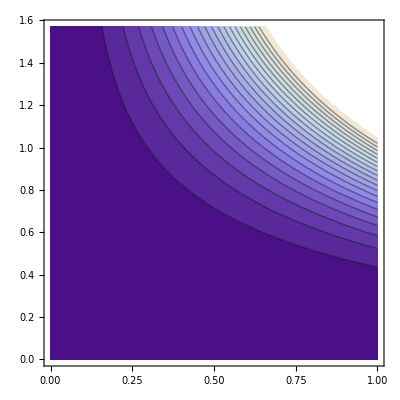

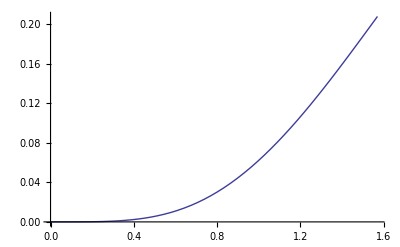

0.207669

```mathematica
(* See Nagataki version with angle dependence *)
toplotfinalpowersasha=finalpowersashanagatakialpha//.{C->1}
ContourPlot[toplotfinalpowersasha,{a,0,1},{he,0,Pi/2},Contours->20]
Plot[(toplotfinalpowersasha//.{a->1}),{he,0,Pi/2}]
N[toplotfinalpowersasha//.{a->1,he->Pi/2}]
```

(0.00160002 a^4 (-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4)/((1+√(1-a^2))^4)+(0.092806 a^2 (-199.846 (2+Cos[he]) Sin[he/2]^4+(-40+60 π^2+5 (-238+33 π^2) Cos[he]+9 (-26+3 π^2) (4 Cos[2 he]+Cos[3 he])) Sin[he/2]^4))/((1+√(1-a^2))^2)

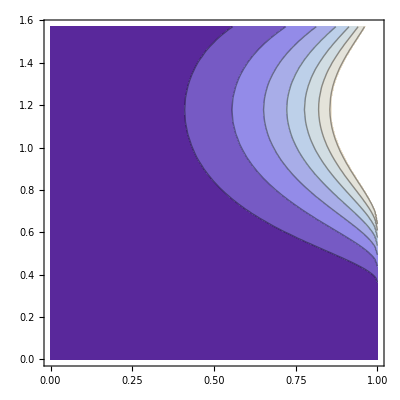

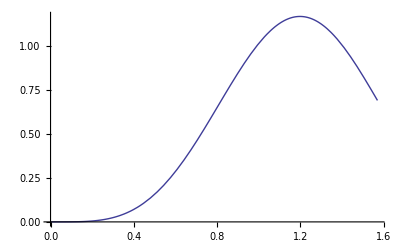

0.692505

```mathematica
(* See omegah version with angle dependence *)
toplotfinalpowersasha=finalpowersasha//.{C->1,OmH->a2OmH[a]}
ContourPlot[toplotfinalpowersasha,{a,0,1},{he,0,Pi/2}]
Plot[(toplotfinalpowersasha//.{a->1}),{he,0,Pi/2}]
N[toplotfinalpowersasha//.{a->1,he->Pi/2}]
```

```mathematica
(* BELOW IS OLDER CODE *)
```

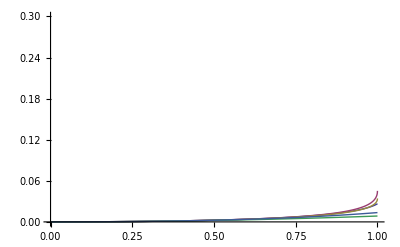

```mathematica
(* The point of this plot is that the top two curves are nearly on top of each other.  These are 
(1) our numerical best-fit solution up to 4th order and (2) Nagataki's expansion in terms of OmegaH:*)
Plot[{(pwrfullanal/.{OmH->a2OmH[a]}/.bestfit/.{C->1}), (* best-fit numerical, 6th order *)
(pwrfullanal/.{OmH->a2OmH[a]}/.{beta->0}/.bestfit/.{C->1}), (* best-fit numerical, 4th order *)
(pwr0anal/.{OmH->a2OmH[a]}/.{C->1}), (* BZ2 *)
(pwr0anal/.{OmH->a/4}/.{C->1}), (* BZ *)
(pwr0anal/.{OmH->a/4})(1+1/45(56-3 Pi^2)a^2)/.{C->1}, (* Nagataki in terms of a, 4th order *)
(pwr0anal(1+alphaNagataki(OmH)^2))/.{OmH->a2OmH[a]}/.{C->1}}, (* Nagataki in terms of OmH, 4th order *)
{a,0,1},PlotRange->{{0,1},{0,0.3}}]
```

```mathematica
data=Table[{a2OmH[datax[[i]]],datay[[i]]-(pwr0anal/.{OmH->a2OmH[datax[[i]]]})/.{C->1}},{i,1,Length[datax]}]
res=Fit[data,{OmH^2,OmH^4,OmH^6},OmH]
clist=CoefficientList[Collect[res-(pwrfullanal-pwr0anal)/.{C->1},OmH],OmH]
Solve[{clist[[5]]==0,clist[[7]]==0},{alpha,beta}]
```

{{0.0250628,-2.79433×10^-7},{0.0505103,-2.53577×10^-7},{0.076768,2.79538×10^-6},{0.133975,0.0000409046},{0.204184,0.000196272},{0.313395,0.000502906},{0.350439,0.000383091},{0.390152,-0.000146252},{0.433804,-0.00162784},{0.467113,-0.00394008},{0.478123,-0.00504612},{0.489367,-0.00634493},{0.492978,-0.00679589}}

-0.00313445 OmH^2+0.21287 OmH^4-1.2943 OmH^6

{0,0,-0.00313445,0,0.21287-0.137078 alpha,0,-1.2943-0.137078 beta}

{{alpha→1.55291,beta→-9.44205}}

```mathematica
Solve[OmH==a/(2(1+Sqrt[1-a^2])),{a}]
```

{{a→(4 OmH)/(1+4 OmH^2)}}